```mathematica
<<mf25.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
H[n_,m_]:=
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m]; (* n+1 instead of n avoids erros in highest order term. Why? *)
djay=x*D[jay,x];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator)^(1/(m-2)),{x,0,n}],x];
Return[answer]]
```

```mathematica
deltaDiamond[n_,m_]:=
Module[{answer},
answer=
Collect[Series[H[n+1,m]^3/J[n+1,m],{x,0,n}],x];
Return[answer]]
```

```mathematica
deltaDiamond[n_,m_]:=
Module[{answer},
answer=
Collect[Series[H[n+2,m]^3/J[n+2,m],{x,0,n}],x];
Return[answer]]
```

```mathematica
deltaDiamondStrike[n_,m_]:=
Module[{f},
f=deltaDiamond[n,m]/.x->(2^6*m^3*x);
c0=Coefficient[f,x,1];
f=Expand[f/c0];
Return[f]]
```

```mathematica
Print[deltaDiamondStrike[6,3]]
```

x-24 x^2+252 x^3-1472 x^4+4830 x^5-6048 x^6

```mathematica
fi=Collect[deltaDiamondStrike[25,3],x];
ex=Exponent[fi,x];
no=0;
For[n=0,n<ex,n++;
cf=Coefficient[fi,x,n];
If[cf≠RamanujanTau[n],no++]];
Print[no]
```

0

```mathematica
stream=OpenWrite["run17aug21no11b"];
For[m=2,m<153,m++;
fi=deltaDiamondStrike[50,m];
Write[stream,{m,Collect[fi,x]}]];
Close[stream]
```

run17aug21no11b

```mathematica
stream=OpenRead["run17aug21no11b"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

151

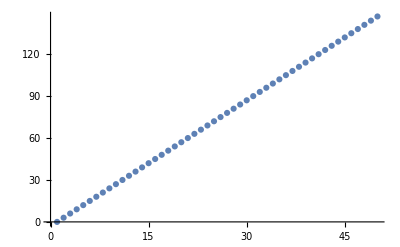

run17aug21no13b

```mathematica
stream=OpenRead["run17aug21no11b"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run17aug21no13b"]; 
degrees={};
For[n=0,n<50,n++;
data={};
For[k=0,k<151,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run17aug21no13b"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

50

```mathematica
stream=OpenRead["run17aug21no13b"];
list=ReadList[stream];
Close[stream];
For[k=0,k<5,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
poly=factorIntoIrreducibleMonics[poly];
Print[{k,n,poly}]]
```

{1,1,{{1,1},{1,1}}}

{2,2,{{-24,1},{1,1},{x,1},{-8/3-2 x+x^2,1}}}

{3,3,{{300,1},{1,1},{-2+x,1},{x,2},{-8/75-(44 x)/15-2 x^2+x^3,1}}}

{4,4,{{-2624,1},{1,1},{1,-1},{-2+x,1},{x,3},{-2176/1107-(8576 x)/1107+(2008 x^2)/1107+(3524 x^3)/1107-(162 x^4)/41+x^5,1}}}

{5,5,{{18126,1},{1,1},{1,-1},{-2+x,1},{x,4},{-2414720/244701-(5280064 x)/244701+(6019424 x^2)/244701-(969104 x^3)/244701-(20872 x^4)/1007+(1242796 x^5)/81567-(17614 x^6)/3021+x^7,1}}}

```mathematica
stream=OpenRead["run17aug21no13b"];
list=ReadList[stream];
Close[stream];
no={};
For[k=0,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
divideby=(x-2)*x^(n-1);
pr=PolynomialRemainder[poly,divideby,x];
If[pr!=0,no=AppendTo[no,n]]];
Print[no]
```

{1}

```mathematica
stream=OpenRead["run17aug21no13b"];
list=ReadList[stream];
Close[stream];
no=0;
For[k=2,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
divideby=(x-2)*x^(n-1);
poly=PolynomialQuotient[poly,divideby,x];
If[Exponent[poly,x]≠2*n-3,no++];
];
Print[no]
```

0

```mathematica
rstream=OpenRead["run17aug21no13b"];
list=ReadList[rstream];
Close[rstream];
poly=list[[50,2]];
poly=Collect[poly,x];
Print[Exponent[poly,x]];
Print[Coefficient[poly,x,147]];
```

147

-14878330606740791629608

```mathematica
(* Polynomial 50 leading term agrees with SageMath's, but the root plot doesn't. *)
```

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

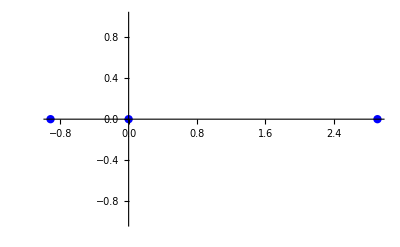

--------------------------------------------------------------

n:  3

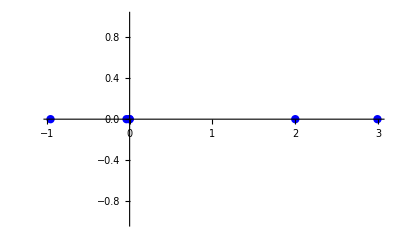

--------------------------------------------------------------

n:  4

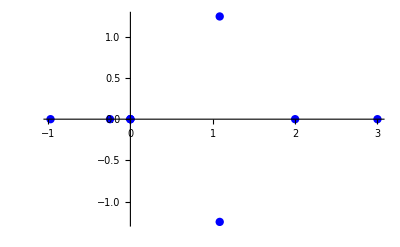

--------------------------------------------------------------

n:  5

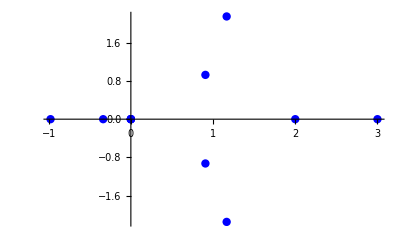

--------------------------------------------------------------

n:  6

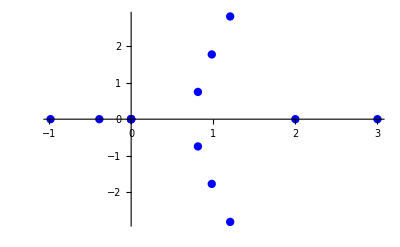

--------------------------------------------------------------

n:  7

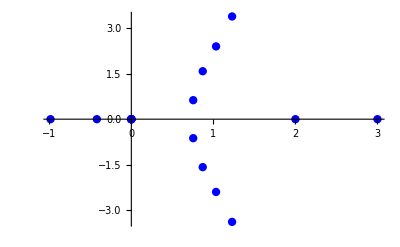

--------------------------------------------------------------

n:  8

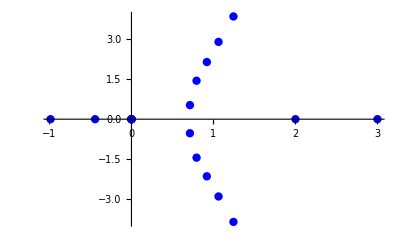

--------------------------------------------------------------

n:  9

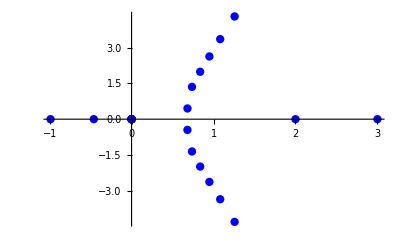

--------------------------------------------------------------

n:  10

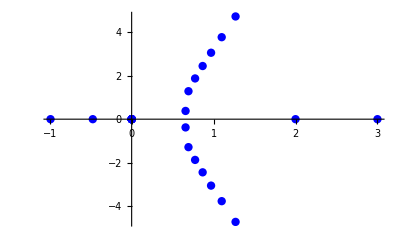

--------------------------------------------------------------

n:  11

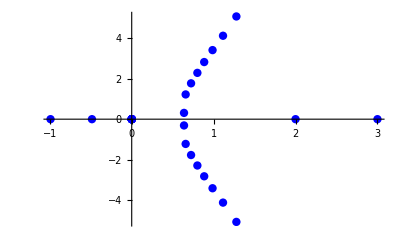

--------------------------------------------------------------

n:  12

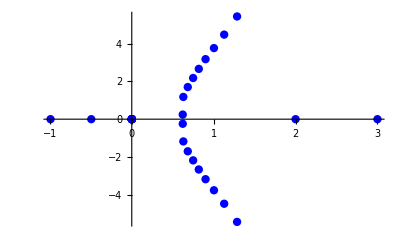

--------------------------------------------------------------

n:  13

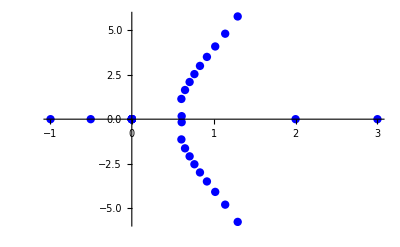

--------------------------------------------------------------

n:  14

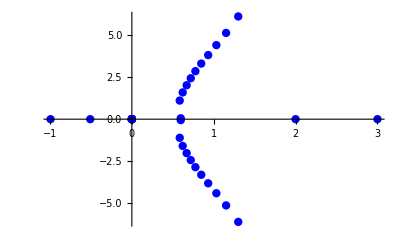

--------------------------------------------------------------

n:  15

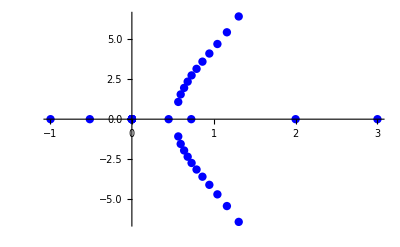

--------------------------------------------------------------

n:  16

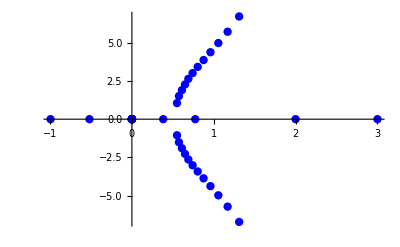

--------------------------------------------------------------

n:  17

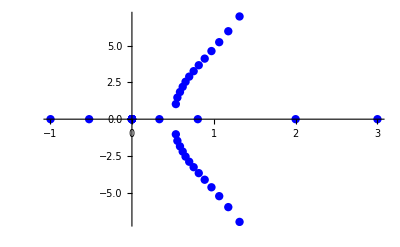

--------------------------------------------------------------

n:  18

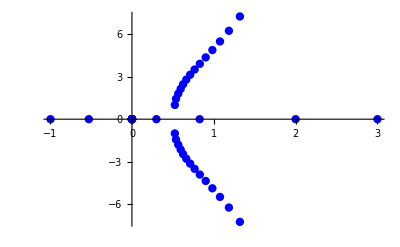

--------------------------------------------------------------

n:  19

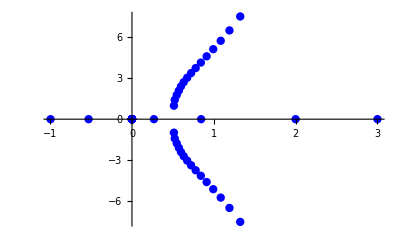

--------------------------------------------------------------

n:  20

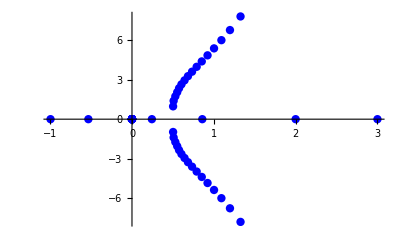

--------------------------------------------------------------

n:  21

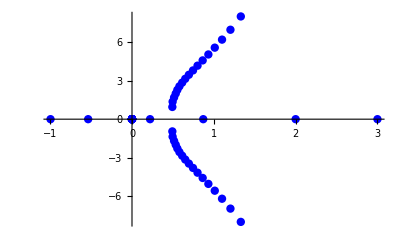

--------------------------------------------------------------

n:  22

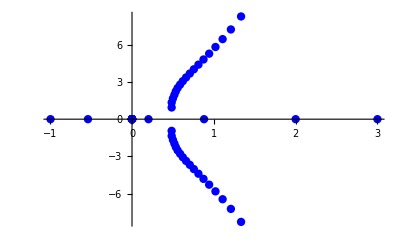

--------------------------------------------------------------

n:  23

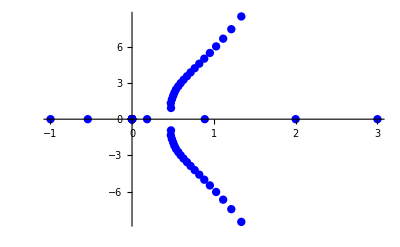

--------------------------------------------------------------

n:  24

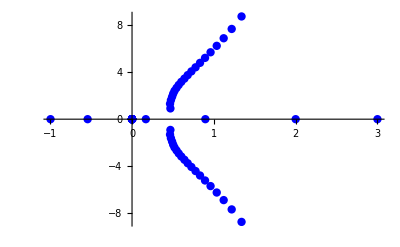

--------------------------------------------------------------

n:  25

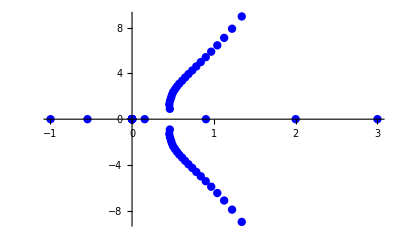

--------------------------------------------------------------

n:  26

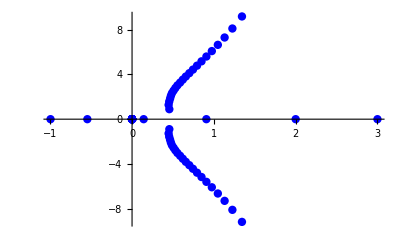

--------------------------------------------------------------

n:  27

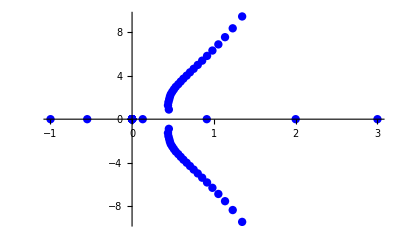

--------------------------------------------------------------

n:  28

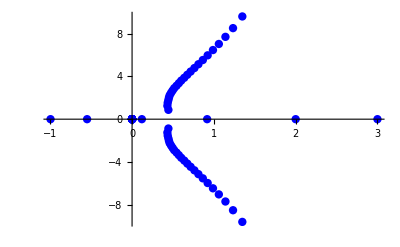

--------------------------------------------------------------

n:  29

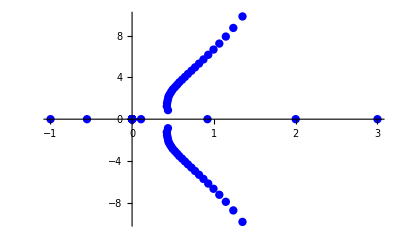

--------------------------------------------------------------

n:  30

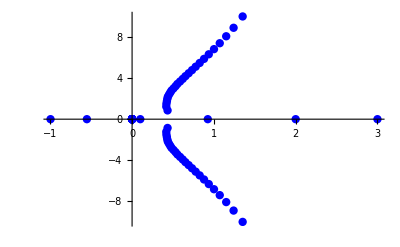

--------------------------------------------------------------

n:  31

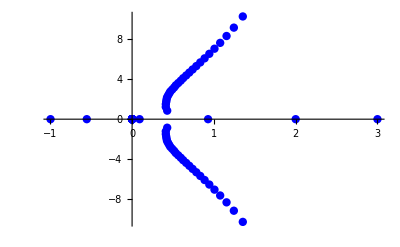

--------------------------------------------------------------

n:  32

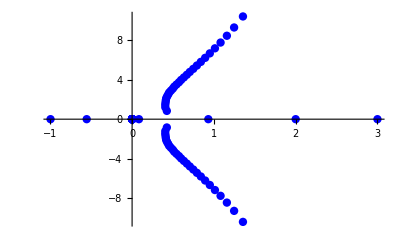

--------------------------------------------------------------

n:  33

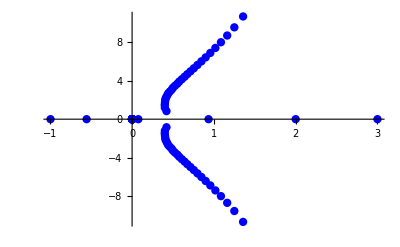

--------------------------------------------------------------

n:  34

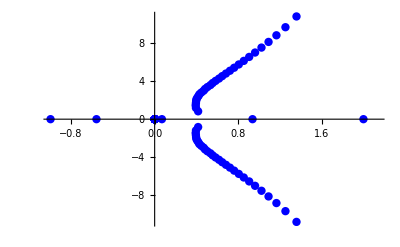

--------------------------------------------------------------

n:  35

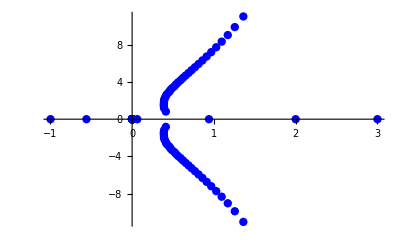

--------------------------------------------------------------

n:  36

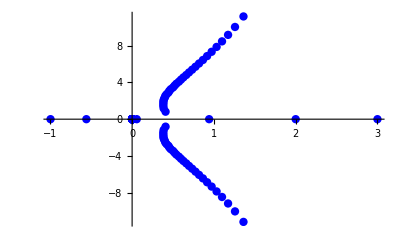

--------------------------------------------------------------

n:  37

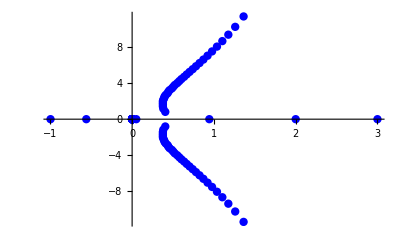

--------------------------------------------------------------

n:  38

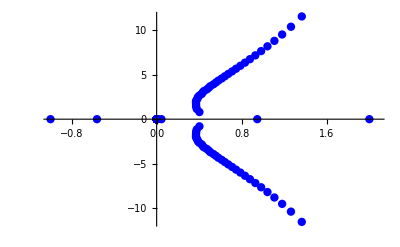

--------------------------------------------------------------

n:  39

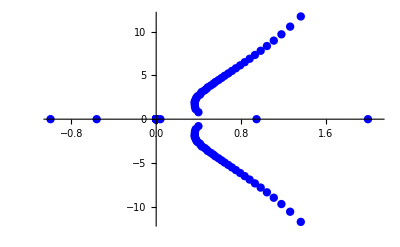

--------------------------------------------------------------

n:  40

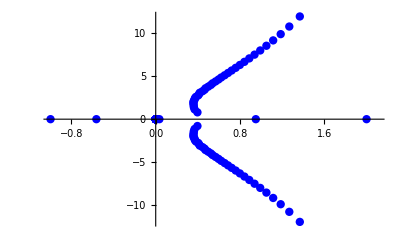

--------------------------------------------------------------

n:  41

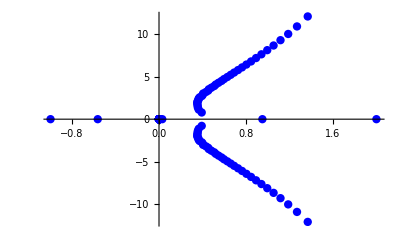

--------------------------------------------------------------

n:  42

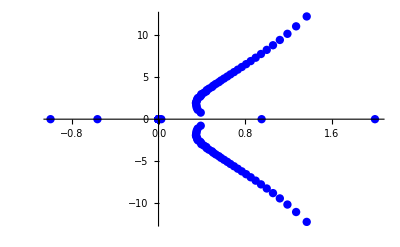

--------------------------------------------------------------

n:  43

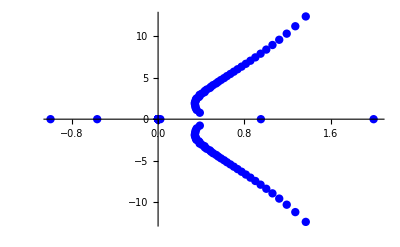

--------------------------------------------------------------

n:  44

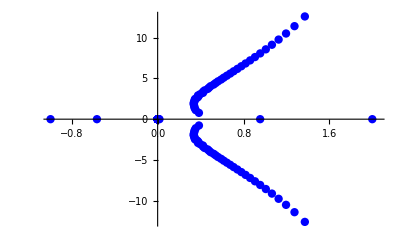

--------------------------------------------------------------

n:  45

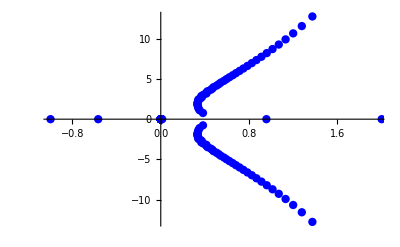

--------------------------------------------------------------

n:  46

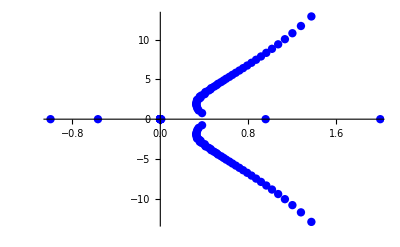

--------------------------------------------------------------

n:  47

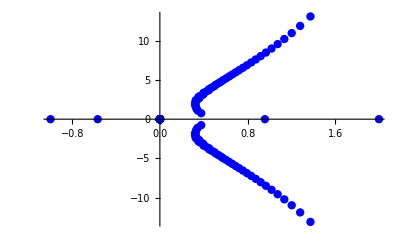

--------------------------------------------------------------

n:  48

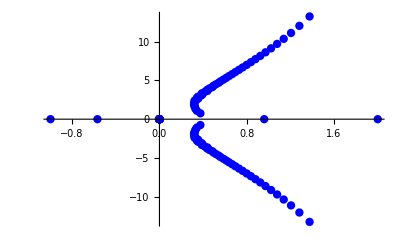

--------------------------------------------------------------

n:  49

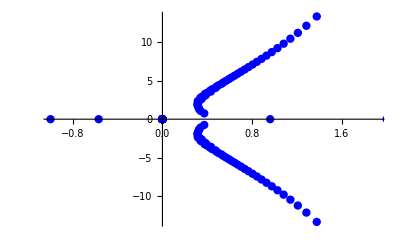

--------------------------------------------------------------

n:  50

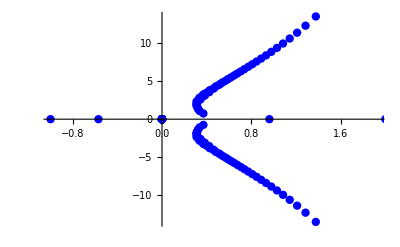

mins

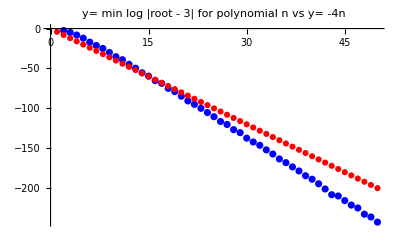

```mathematica
rstream=OpenRead["run17aug21no13b"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
data={};
degrees={};
no=0;
precision=300;
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-4*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -4n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

-Graphics-

--------------------------------------------------------------

n:  3

-Graphics-

--------------------------------------------------------------

n:  4

-Graphics-

--------------------------------------------------------------

n:  5

-Graphics-

--------------------------------------------------------------

n:  6

-Graphics-

--------------------------------------------------------------

n:  7

-Graphics-

--------------------------------------------------------------

n:  8

-Graphics-

--------------------------------------------------------------

n:  9

-Graphics-

--------------------------------------------------------------

n:  10

-Graphics-

--------------------------------------------------------------

n:  11

-Graphics-

--------------------------------------------------------------

n:  12

-Graphics-

--------------------------------------------------------------

n:  13

-Graphics-

--------------------------------------------------------------

n:  14

-Graphics-

--------------------------------------------------------------

n:  15

-Graphics-

--------------------------------------------------------------

n:  16

-Graphics-

--------------------------------------------------------------

n:  17

-Graphics-

--------------------------------------------------------------

n:  18

-Graphics-

--------------------------------------------------------------

n:  19

-Graphics-

--------------------------------------------------------------

n:  20

-Graphics-

--------------------------------------------------------------

n:  21

-Graphics-

--------------------------------------------------------------

n:  22

-Graphics-

--------------------------------------------------------------

n:  23

-Graphics-

--------------------------------------------------------------

n:  24

-Graphics-

--------------------------------------------------------------

n:  25

-Graphics-

--------------------------------------------------------------

n:  26

-Graphics-

--------------------------------------------------------------

n:  27

-Graphics-

--------------------------------------------------------------

n:  28

-Graphics-

--------------------------------------------------------------

n:  29

-Graphics-

--------------------------------------------------------------

n:  30

-Graphics-

--------------------------------------------------------------

n:  31

-Graphics-

--------------------------------------------------------------

n:  32

-Graphics-

--------------------------------------------------------------

n:  33

-Graphics-

--------------------------------------------------------------

n:  34

-Graphics-

--------------------------------------------------------------

n:  35

-Graphics-

--------------------------------------------------------------

n:  36

-Graphics-

--------------------------------------------------------------

n:  37

-Graphics-

--------------------------------------------------------------

n:  38

-Graphics-

--------------------------------------------------------------

n:  39

-Graphics-

--------------------------------------------------------------

n:  40

-Graphics-

--------------------------------------------------------------

n:  41

-Graphics-

--------------------------------------------------------------

n:  42

-Graphics-

--------------------------------------------------------------

n:  43

-Graphics-

--------------------------------------------------------------

n:  44

-Graphics-

--------------------------------------------------------------

n:  45

-Graphics-

--------------------------------------------------------------

n:  46

-Graphics-

--------------------------------------------------------------

n:  47

-Graphics-

--------------------------------------------------------------

n:  48

-Graphics-

--------------------------------------------------------------

n:  49

-Graphics-

--------------------------------------------------------------

n:  50

-Graphics-

mins

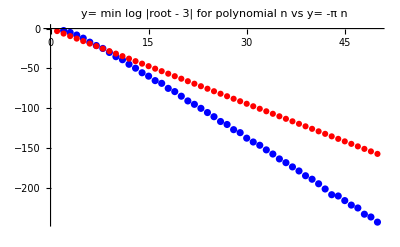

```mathematica
rstream=OpenRead["run17aug21no13b"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
data={};
degrees={};
no=0;
precision=300;
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-Pi*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -π n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```